This the analytical solution to the differential equation:

```mathematica
a=3.5; m=2; τ=1;
f[η_]:= η^(1/m)(((m-1)/(2 m (m+1))) (a^((m+1)/m)-η^((m+1)/m)))^(1/(m-1))
```

```mathematica
u1[x_,t_]:= Piecewise[{{(t+τ)^(-1/m) f[x (t+τ)^(-1/(2 m))],0≤ x ≤ a(t+τ)^(1/(2m))},
{0,a(t+τ)^(1/(2m))< x  }}]
```

```mathematica
u1[0.1,0.1]
```

0.161816

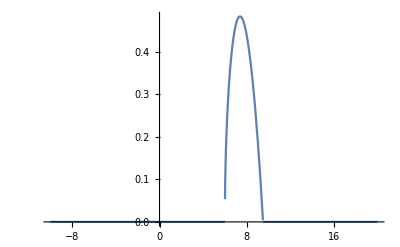

```mathematica
Plot[u1[x-6,0], {x,-10,20}, PlotRange->Full]
```

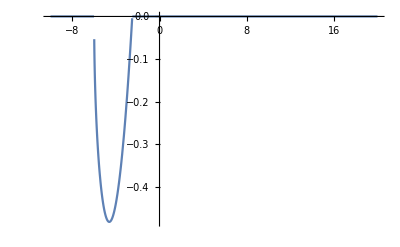

```mathematica
Plot[-u1[6+x,0],{x,-10,20}, PlotRange->Full]
```

Seems that Mathematica cant solve equation of type:    ∇^2 (u |u|)=u_t

```mathematica
Clear[u]
ndsol=NDSolve[{D[u[t,x],t]==D[u[t,x],x,x]u[t,x] ,u[0,x]==u1[x,0],u[t,20]==u1[20,t],u[t,0]==u1[0,t]},u,{x,0,20},{t,0.0,8.94}]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{u→InterpolatingFunction[{{0., 8.94}, {0., 20.}}, <>]}}

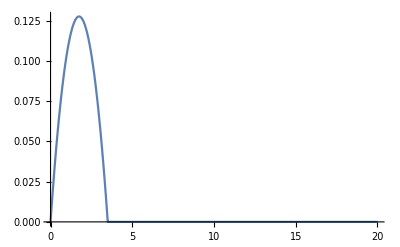

```mathematica
num=Plot[Evaluate[u[8.93,x]/.ndsol], {x,0,20},PlotRange->Full]
```

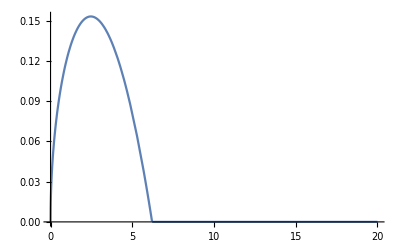

```mathematica
ana=Plot[u1[x,8.93],{x,0,20}]
```

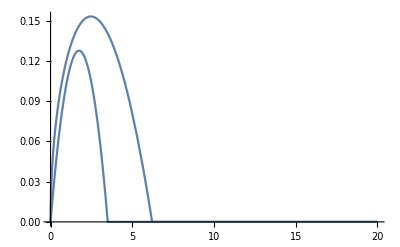

```mathematica
Show[{ana,num}]
```